Hamiltonian simulation in QSVT is approximated with the Jacobi Anger expansion. We follow the expressions given in GSLW 2019 “qsvt...beyond”. (Mainly because they address some small technical problems with a proof from Low and Chuang.) We will also consider different expressions for truncating n, from Haah 2019 “product decomp.. “ and Dong  et Al. “efficient”. Martyn et Al.  “grand” uses exactly the same expression as Gilyen et Al.,

```mathematica
rscaling[t_, ϵ_]:=Abs[t]+Log[1/ϵ]/Log[ⅇ+Log[1/ϵ]/Abs[t]];
rh19[t_,ϵ_]:=Floor[ⅇ/2*Abs[t]+Log[1/ϵ]];
rgslw19[t_, ϵ_]:=Floor[rscaling[ⅇ/2*Abs[t], 5/4*ϵ]];
rdmwl21[t_, ϵ_]:=Floor[1.4*Abs[t]+ Log10[1/ϵ]];
```

As a sanity check, confirm these produce the expected order of magnitude for ‘realistic’ cases.

```mathematica
rh19[10^(3), 10^(-16)]
rgslw19[10^(3), 10^(-16)]
rdmwl21[10^(3), 10^(-16)]
```

1395

1395

1416

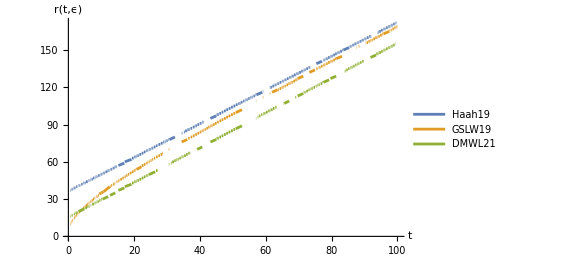

```mathematica
Plot[{rh19[t, 10^(-16)], rgslw19[t, 10^(-16)], rdmwl21[t, 10^(-16)]}, {t,0.5, 100}, PlotLegends->{"Haah19", "GSLW19", "DMWL21"},AxesLabel->{t, r[t, ϵ]}]
```

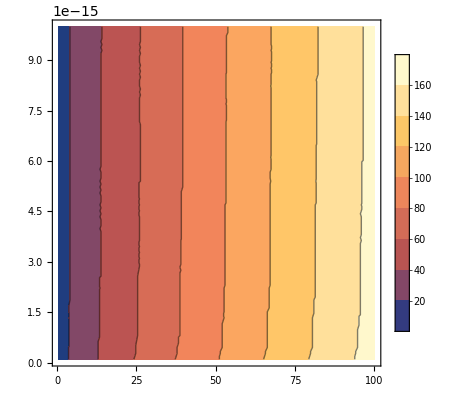

```mathematica
ContourPlot[rh19[t, ϵ]=rgslw19[t,ϵ],{t,0.5,100},{ϵ,10^(-16),10^(-14)}, PlotLegends->Automatic]
```

```mathematica
ContourPlot[rdmwl21[t, ϵ]=rgslw19[t,ϵ],{t,0.5,100},{ϵ,10^(-16),10^(-14)}, PlotLegends->Automatic]
```

-Graphics-

From the above contour plots, it looks like we can straightforwardly use the linear plot above and assume there is some ‘crossing point’ after which DMWL21<RGSL19<Haah19

Now actually code the function

```mathematica
cfgslw19[t_, r_, λ_]:=BesselJ[0, t]+2*Sum[(-1)^j*BesselJ[2*j, t]*ChebyshevT[2*j, λ], {j, 1, r}];
```

```mathematica
sfgslw19[t_, r_, λ]:=2*Sum[(-1)^j*BesselJ[2*j+1, t]*ChebyshevT[2*j+1, λ], {j, 0, r}];
```

```mathematica
τ=50;
```

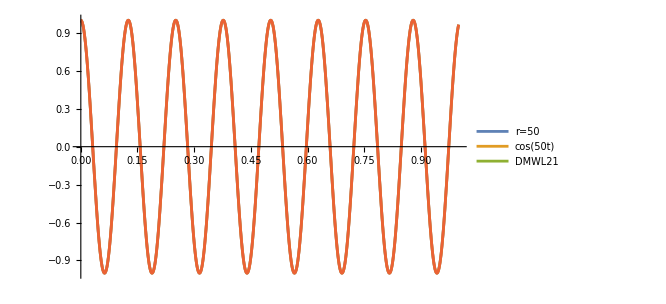

```mathematica
Plot[{cfgslw19[τ, 50, λ],Cos[τ*λ], , cfgslw19[τ,rdmwl21[τ, 10^(-16)],  λ] }, {λ, 0, 1}, PlotLegends->{"r=50", "cos(50t)", "DMWL21"}]
```

```mathematica
coeffgslw19[t_, j_]:=If[j==0, N[BesselJ[0, t]],If[EvenQ[j], N[2*(-1)^(j/2)*BesselJ[j, t]],I*N[2*(-1)^((j-1)/2)*BesselJ[j, t]]]] ;
```

```mathematica
clistgslw19[t_, r_]:=Table[coeffgslw19[t, j],{j,0,2*r+1}];
```

```mathematica
A=clistgslw19[τ,rdmwl21[τ,10^(-16) ]]
```

General::munfl: 0.0248489 1.3779×10^-307 is too small to represent as a normalized machine number; precision may be lost.

{0.0558123,0.-0.195024 ⅈ,0.119426,0.-0.18547 ⅈ,0.141682,0.-0.1628 ⅈ,0.174242,0.-0.120982 ⅈ,0.208117,0.-0.0543849 ⅈ,0.227696,0.+0.0366934 ⅈ,0.211551,0.+0.138238 ⅈ,0.139667,0.+0.216451 ⅈ,0.00979632,0.+0.222721 ⅈ,-0.141654,0.+0.12073 ⅈ,-0.233409,0.-0.0659969 ⅈ,-0.177971,0.-0.222612 ⅈ,0.0268314,0.-0.196854 ⅈ,0.223685,0.+0.0357788 ⅈ,0.185044,0.+0.243028 ⅈ,-0.0968685,0.+0.126786 ⅈ,-0.254083,0.-0.19844 ⅈ,0.00785839,0.-0.187753 ⅈ,0.270712,0.+0.202073 ⅈ,-0.0283556,0.+0.158972 ⅈ,-0.276353,0.-0.283192 ⅈ,0.188082,0.+0.0327858 ⅈ,0.13169,0.+0.264561 ⅈ,-0.344519,0.-0.369354 ⅈ,0.349867,0.+0.30239 ⅈ,-0.242818,0.-0.183246 ⅈ,0.131003,0.+0.0892413 ⅈ,-0.0581881,0.-0.036445 ⅈ,0.0219909,0.+0.0128146 ⅈ,-0.00722637,0.-0.0039506 ⅈ,0.00209704,0.+0.0010823 ⅈ,-0.000543767,0.-0.000266244 ⅈ,0.000127168,0.+0.0000593055 ⅈ,-0.0000270265,0.-0.0000120446 ⅈ,5.25291×10^-6,0.+2.24335×10^-6 ⅈ,-9.38734×10^-7,0.-3.85106×10^-7 ⅈ,1.54966×10^-7,0.+6.11963×10^-8 ⅈ,-2.37272×10^-8,0.-9.03631×10^-9 ⅈ,3.38171×10^-9,0.+1.24409×10^-9 ⅈ,-4.50089×10^-10,0.-1.60187×10^-10 ⅈ,5.61031×10^-11,0.+1.93425×10^-11 ⅈ,-6.56654×10^-12,0.-2.19577×10^-12 ⅈ,7.23406×10^-13,0.+2.34877×10^-13 ⅈ,-7.51745×10^-14,0.-2.37236×10^-14 ⅈ,7.38369×10^-15,0.+2.26698×10^-15 ⅈ,-6.86747×10^-16,0.-2.05312×10^-16 ⅈ,6.05881×10^-17,0.+1.76523×10^-17 ⅈ,-5.07856×10^-18,0.-1.44305×10^-18 ⅈ,4.05047×10^-19,0.+1.12327×10^-19 ⅈ,-3.07815×10^-20,0.-8.33672×10^-21 ⅈ,2.23185×10^-21,0.+5.90703×10^-22 ⅈ,-1.54586×10^-22,0.-4.00063×10^-23 ⅈ,1.02401×10^-23,0.+2.59277×10^-24 ⅈ,-6.49466×10^-25,0.-1.60968×10^-25 ⅈ,3.94795×10^-26,0.+9.58301×10^-27 ⅈ,-2.30241×10^-27,0.-5.47602×10^-28 ⅈ,1.28943×10^-28,0.+3.00628×10^-29 ⅈ,-6.94074×10^-30,0.-1.58699×10^-30 ⅈ,3.59399×10^-31,0.+8.0623×10^-32 ⅈ,-1.79169×10^-32,0.-3.94486×10^-33 ⅈ,8.60605×10^-34,0.+1.86046×10^-34 ⅈ,-3.98585×10^-35,0.-8.46337×10^-36 ⅈ,1.78125×10^-36,0.+3.71622×10^-37 ⅈ,-7.68617×10^-38,0.-1.57611×10^-38 ⅈ,3.20452×10^-39,0.+6.46063×10^-40 ⅈ,-1.29168×10^-40,0.-2.56116×10^-41 ⅈ,5.03677×10^-42,0.+9.82496×10^-43 ⅈ,-1.9011×10^-43,0.-3.64925×10^-44 ⅈ,6.94955×10^-45,0.+1.31309×10^-45 ⅈ,-2.46175×10^-46,0.-4.57967×10^-47 ⅈ,8.45458×10^-48,0.+1.54898×10^-48 ⅈ,-2.81657×10^-49,0.-5.08327×10^-50 ⅈ,9.10626×10^-51,0.+1.61933×10^-51 ⅈ,-2.85861×10^-52,0.-5.00983×10^-53 ⅈ,8.71693×10^-54,0.+1.50591×10^-54 ⅈ,-2.58319×10^-55,0.-4.40003×10^-56 ⅈ,7.44251×10^-57,0.+1.25017×10^-57 ⅈ,-2.0856×10^-58,0.-3.45559×10^-59 ⅈ,5.68678×10^-60,0.+9.29573×10^-61 ⅈ,-1.50936×10^-61,0.-2.43455×10^-62 ⅈ,3.90102×10^-63,0.+6.20999×10^-64 ⅈ,-9.82148×10^-65,0.-1.54332×10^-65 ⅈ,2.40961×10^-66,0.+3.73823×10^-67 ⅈ,-5.76283×10^-68,0.-8.82818×10^-69 ⅈ,1.34398×10^-69,0.+2.03336×10^-70 ⅈ,-3.05743×10^-71,0.-4.56914×10^-72 ⅈ,6.78684×10^-73,0.+1.00201×10^-73 ⅈ}

This is much better  - now we need to check that the plot matches what is expected

```mathematica
f2gslw19[t_, r_, λ_]=ChebyshevT[Range[0,2*r+1], λ].clistgslw19[t, r]
```

Range::range: Range specification in Range[0,1+2 r] does not have appropriate bounds.

Table::iterb: Iterator {j,0,1+2 r} does not have appropriate bounds.

ChebyshevT[Range[0,1+2 r],λ].Table[coeffgslw19[t,j],{j,0,1+2 r}]

```mathematica
f2gslw19[t,2 , λ]
```

BesselJ[0.,t]+(0.+2. ⅈ) λ BesselJ[1.,t]-2. (-1+2 λ^2) BesselJ[2.,t]-(0.+2. ⅈ) (-3 λ+4 λ^3) BesselJ[3.,t]+2. (1-8 λ^2+8 λ^4) BesselJ[4.,t]+(0.+2. ⅈ) (5 λ-20 λ^3+16 λ^5) BesselJ[5.,t]

General::munfl: 0.0248489 1.3779×10^-307 is too small to represent as a normalized machine number; precision may be lost.

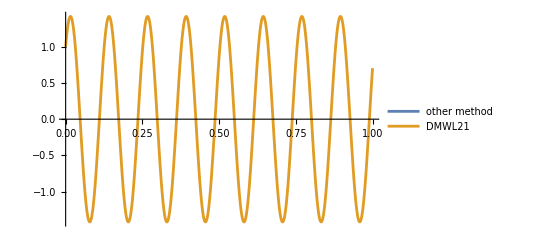

```mathematica
Plot[{f2gslw19[τ, rdmwl21[τ, 10^(-16)], λ], cfgslw19[τ,rdmwl21[τ, 10^(-16)],  λ] }, {λ, 0, 1}, PlotLegends->{"other method","DMWL21"}]
```